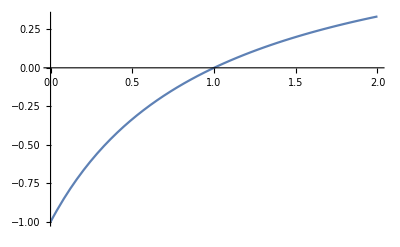

```mathematica
Plot[(x-1)/(x+1),{x,0,2}]
```

```mathematica
def={γ-> (e-Y)-1/2 B 1/j  B ,βc-> A-1/2 B ⅇ^(-ⅈ (κ))  B ,β->A-1/2 B ⅇ^(ⅈ (κ))  B ,α-> (e+Y)-1/2 B j  B ,τ-> q^2/Subscript[k, 0]^2 };
{ⅇ^(ⅈ (r-Subscript[r, c]))-> j}
preset = {e-> 1,e3-> 1, Y-> 0,r->0,rc->0,A-> 0.5};
cholpreset={e-> 1,e3-> 1, Y-> 0,B->0,Bc-> 0,r-> 0,rc-> 0,A-> 0.5};
```

{ⅇ^(ⅈ (r-r_c))→j}

```mathematica
Ap=ⅇ^(ⅈ(q z-ϕ)n)ⅇ^(ⅈ ϕ);
Am=(n^2 τ-α)/β ⅇ^(ⅈ (q z -ϕ)(n-2))ⅇ^(-ⅈ ϕ);
Apc=ⅇ^(-ⅈ(q z-ϕ)n)ⅇ^(-ⅈ ϕ);
Amc=(n^2 τ-α)/βc ⅇ^(-ⅈ (q z -ϕ)(n-2))ⅇ^(ⅈ ϕ);
```

```mathematica
ξ2=FullSimplify[(Am Amc-Ap Apc)/(Am Amc+Ap Apc)]
```

1-(2 β βc)/(β βc+(α-n^2 τ)^2)

```mathematica
σ11=(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.def
σ22=(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β βc-α γ)))/(2 β βc-2 α γ)/.def
```

(-n^2 (e-B^2/(2 j)-Y)-(-2+n)^2 (e-(B^2 j)/2+Y)+√((n^2 (e-B^2/(2 j)-Y)+(-2+n)^2 (e-(B^2 j)/2+Y))^2+4 (-2+n)^2 n^2 ((A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-(e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))))/(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-2 (e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))

(-n^2 (e-B^2/(2 j)-Y)-(-2+n)^2 (e-(B^2 j)/2+Y)-√((n^2 (e-B^2/(2 j)-Y)+(-2+n)^2 (e-(B^2 j)/2+Y))^2+4 (-2+n)^2 n^2 ((A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-(e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))))/(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-2 (e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))

```mathematica
ξ2/.def//FullSimplify
```

1-(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ)))/(A^2-A B^2 Cos[κ]+1/4 B^4 Cos[κ]^2+1/4 B^4 Sin[κ]^2+(e-(B^2 j)/2+Y-(n^2 q^2)/k_0^2)^2)

```mathematica
(*строим ξ2 на оболочке*)
```

```mathematica
(*первая и вторая ветиви*)
```

```mathematica
Manipulate[{Plot[{1-(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ)))/(A^2-A B^2 Cos[κ]+1/4 B^4 Cos[κ]^2+1/4 B^4 Sin[κ]^2+(e-(B^2 j)/2+Y-n^2 /(-n^2 (e-B^2/(2 j)-Y)-(-2+n)^2 (e-(B^2 j)/2+Y)+√((n^2 (e-B^2/(2 j)-Y)+(-2+n)^2 (e-(B^2 j)/2+Y))^2+4 (-2+n)^2 n^2 ((A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-(e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))))/(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-2 (e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y)))^2)},{n,0,M}],Plot[{1-(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ)))/(A^2-A B^2 Cos[κ]+1/4 B^4 Cos[κ]^2+1/4 B^4 Sin[κ]^2+(e-(B^2 j)/2+Y-n^2 /(-n^2 (e-B^2/(2 j)-Y)-(-2+n)^2 (e-(B^2 j)/2+Y)-√((n^2 (e-B^2/(2 j)-Y)+(-2+n)^2 (e-(B^2 j)/2+Y))^2+4 (-2+n)^2 n^2 ((A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-(e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))))/(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-2 (e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y)))^2)},{n,0,M}],Plot[{(-n^2 (e-B^2/(2 j)-Y)-(-2+n)^2 (e-(B^2 j)/2+Y)-√((n^2 (e-B^2/(2 j)-Y)+(-2+n)^2 (e-(B^2 j)/2+Y))^2+4 (-2+n)^2 n^2 ((A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-(e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))))/(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-2 (e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y)),(-n^2 (e-B^2/(2 j)-Y)-(-2+n)^2 (e-(B^2 j)/2+Y)+√((n^2 (e-B^2/(2 j)-Y)+(-2+n)^2 (e-(B^2 j)/2+Y))^2+4 (-2+n)^2 n^2 ((A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-(e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))))/(2 (A-1/2 B^2 ⅇ^(-ⅈ κ)) (A-1/2 B^2 ⅇ^(ⅈ κ))-2 (e-B^2/(2 j)-Y) (e-(B^2 j)/2+Y))},{n,-2,4}],Plot[{(e+Y)-1/2 B j  B ,A-1/2 B  B , (e-Y)-1/2 B 1/j  B  },{n,0,10}]},{M,10,40},{κ,0,π/2},{j,1,2},{B,0,10},{A,-0.5,1},{Y,0,1},{e,1,2}]
```

```mathematica
FullSimplify[A-1/2 B  B/.A-> 0.6/.B-> 1.1]
```

-0.005

```mathematica
Manipulate[{Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M,M}],Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M,M}],Plot[{100(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),100(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,1-m,1+m}]},{m,5,0},{M,2,1000},{α,0.1,2},{β,0,3},{γ,0.1,2},{κ,0,π/2},{j,1,2},{B,0,10},{A,-0.5,1},{Y,0.1,1},{e,1,2}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

```mathematica
D[1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2),n]//Simplify
```

(32 (-2+n) n β^2 (β^2-α γ) (α-(2 n^2 (β^2-α γ))/(-(-2+n)^2 α-n^2 γ+√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)))) ((-2+n)^2 α^2+2 n^2 β^2-α (n^2 γ+√((-2+n)^4 α^2-2 (-2+n)^2 n^2 α γ+n^2 (4 (-2+n)^2 β^2+n^2 γ^2)))))/(√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)) (4 α-4 n α+n^2 α+n^2 γ-√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)))^2 (β^2+(α-(2 n^2 (β^2-α γ))/(-(-2+n)^2 α-n^2 γ+√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ))))^2)^2)

```mathematica
Manipulate[{Plot[{(32 (-2+n) n β^2 (β^2-α γ) (α-(2 n^2 (β^2-α γ))/(-(-2+n)^2 α-n^2 γ+√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)))) ((-2+n)^2 α^2+2 n^2 β^2-α (n^2 γ+√((-2+n)^4 α^2-2 (-2+n)^2 n^2 α γ+n^2 (4 (-2+n)^2 β^2+n^2 γ^2)))))/(√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)) (4 α-4 n α+n^2 α+n^2 γ-√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)))^2 (β^2+(α-(2 n^2 (β^2-α γ))/(-(-2+n)^2 α-n^2 γ+√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ))))^2)^2)},{n,-M,M}],Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M,M}], Plot[{(4 α-4 n α+n^2 α+n^2 γ-√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ)))^2 },{n,-M,M}],Plot[{(β^2+(α-(2 n^2 (β^2-α γ))/(-(-2+n)^2 α-n^2 γ+√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ))))^2)^2},{n,-M,M}],Plot[{√(((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (β^2-α γ))},{n,-M,M}],Plot[{100(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),100(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,1-m,1+m}]},{m,5,0},{M,2,1000},{α,0.1,2},{β,0,3},{γ,0.1,2},{κ,0,π/2},{j,1,2},{B,0,10},{A,-0.5,1},{Y,0.1,1},{e,1,2}]
```

```mathematica
Solve[((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (0-α γ)==0,n]
```

{{n→(2 (α-√α √γ))/(α-γ)},{n→(2 (α-√α √γ))/(α-γ)},{n→(2 (α+√α √γ))/(α-γ)},{n→(2 (α+√α √γ))/(α-γ)}}

```mathematica
Solve[D[((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (0-α γ),n]==0,n]
```

{{n→(2 α)/(α-γ)},{n→(2 (α-√α √γ))/(α-γ)},{n→(2 (α+√α √γ))/(α-γ)}}

```mathematica
Solve[D[((-2+n)^2 α+n^2 α)^2+4 (-2+n)^2 n^2 (β^2-α^2),n]==0,n]
```

{{n→1},{n→(β^2-√(-2 α^2 β^2+β^4))/β^2},{n→(β^2+√(-2 α^2 β^2+β^4))/β^2}}

```mathematica
Simplify[1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)/.γ-> α]
```

1-(2 β^2)/(β^2+(α-(n^2 (α^2-β^2))/((2-2 n+n^2) α-√(4 (-1+n)^2 α^2+(-2+n)^2 n^2 β^2)))^2)

```mathematica
Series[Assuming[{α>0,β>0},D[1-(2 β^2)/(β^2+(α-(n^2 (α^2-β^2))/((2-2 n+n^2) α-√(4 (-1+n)^2 α^2+(-2+n)^2 n^2 β^2)))^2),n]/.n-> 1+ϵ//Simplify],{ϵ,0,1}]
```

-(2 ((-α^2+β^2) (α-√(β^2)) (β^3-α β √(β^2))^2))/(√(β^2) (α^2 β^2+β^4-2 α (β^2)^(3/2))^2)+O[ϵ]^2

```mathematica
Assuming[{α>0,β>0},-(2 ((-α^2+β^2) (α-√(β^2)) (β^3-α β √(β^2))^2))/(√(β^2) (α^2 β^2+β^4-2 α (β^2)^(3/2))^2)//Simplify]
```

(2 (α+β))/β

```mathematica
Series[Assuming[{α>0,β>0},1-(2 β^2)/(β^2+(α-(n^2 (α^2-β^2))/((2-2 n+n^2) α-√(4 (-1+n)^2 α^2+(-2+n)^2 n^2 β^2)))^2)/.n-> 1+ϵ//Simplify],{ϵ,0,1}]
```

(2 (-α^2+β^2) (-α+√(β^2))^2 (β^2-α √(β^2)) ϵ)/(β^2 (α^2+β^2-2 α √(β^2))^2)+O[ϵ]^2

```mathematica
Assuming[{α>0,β>0},(2 (-α^2+β^2) (-α+√(β^2))^2 (β^2-α √(β^2)) ϵ)/(β^2 (α^2+β^2-2 α √(β^2))^2)//Simplify]
```

(2 (α+β) ϵ)/β

```mathematica
Series[Assuming[{α>0,β>0},1-(2 β^2)/(β^2+(α-(n^2 (α^2-β^2))/((2-2 n+n^2) α+√(4 (-1+n)^2 α^2+(-2+n)^2 n^2 β^2)))^2)/.n-> 1+ϵ//Simplify],{ϵ,0,1}]
```

(2 (-α^2+β^2) (α+√(β^2))^2 (β^2+α √(β^2)) ϵ)/(β^2 (α^2+β^2+2 α √(β^2))^2)+O[ϵ]^2

```mathematica
Assuming[{α>0,β>0},(2 (-α^2+β^2) (α+√(β^2))^2 (β^2+α √(β^2)) ϵ)/(β^2 (α^2+β^2+2 α √(β^2))^2)//Simplify]
```

(2 (-α+β) ϵ)/β

```mathematica
Manipulate[{Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M,M}],Plot[{1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)},{n,-M,M}],Plot[{100(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),100(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,1-m,1+m}]},{m,5,0},{M,2,1000},{α,0.1,2},{β,0,3},{γ,0.1,2}]
```

```mathematica
Manipulate[{Plot[{100(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),100(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,1-m,1+m}]},{m,10,0},{M,2,1000},{α,0.1,2},{β,0,3},{γ,0.1,2}]
```

```mathematica
Solve[((-2+n)^2 α+n^2 γ)^2+4 (-2+n)^2 n^2 (0-α γ)==0,n]
```

{{n→(2 (α-√α √γ))/(α-γ)},{n→(2 (α-√α √γ))/(α-γ)},{n→(2 (α+√α √γ))/(α-γ)},{n→(2 (α+√α √γ))/(α-γ)}}

```mathematica
Series[Assuming[{α>0,β>0},1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)/. n->(2 (α-√α √γ))/(α-γ)+ϵ//Simplify],{ϵ,0,1}];
```

```mathematica
Series[Assuming[{α>0,β>0},1-(2 β β)/(β β+(α-n^2/((-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)))^2)/. n->(2 (α-√α √γ))/(α-γ)+ϵ//Simplify],{ϵ,0,1}]
```

(α-γ)/(α+γ)+(2 √α β^2 (√α+√γ)^2 (β^2-α γ) (α+(8 α (β^2-α γ))/((√α+√γ)^2 ((8 α γ)/(√α+√γ)^2+8 √((α β^2 γ)/(√α+√γ)^4)))) ϵ)/(√γ (α γ+α √((α β^2 γ)/(√α+√γ)^4)+2 √α √γ √((α β^2 γ)/(√α+√γ)^4)+γ √((α β^2 γ)/(√α+√γ)^4)) (β^2+(α+(8 α (β^2-α γ))/((√α+√γ)^2 ((8 α γ)/(√α+√γ)^2+8 √((α β^2 γ)/(√α+√γ)^4))))^2)^2)+O[ϵ]^2

```mathematica
Assuming[{α>0,β>0,γ>0},(α-γ)/(α+γ)+(2 √α β^2 (√α+√γ)^2 (β^2-α γ) (α+(8 α (β^2-α γ))/((√α+√γ)^2 ((8 α γ)/(√α+√γ)^2+8 √((α β^2 γ)/(√α+√γ)^4)))) ϵ)/(√γ (α γ+α √((α β^2 γ)/(√α+√γ)^4)+2 √α √γ √((α β^2 γ)/(√α+√γ)^4)+γ √((α β^2 γ)/(√α+√γ)^4)) (β^2+(α+(8 α (β^2-α γ))/((√α+√γ)^2 ((8 α γ)/(√α+√γ)^2+8 √((α β^2 γ)/(√α+√γ)^4))))^2)^2)+O[ϵ]^2//Simplify]
```

(α-γ)/(α+γ)-(2 ((-β^2+α γ) (√(α^3 γ)+√(α γ^3)+α (β+2 γ)+β (γ+2 √(α γ))) (α^2 γ+β γ √(α γ)+α β (2 γ+√(α γ))+α γ (γ+2 √(α γ)))^2) ϵ)/(β (√α+√γ)^4 √(α γ) (α+γ)^2 (β^2+α γ+(2 β (√(α γ^3)+α (2 γ+√(α γ))))/(√α+√γ)^2)^2)+O[ϵ]^2

```mathematica
(α-γ)/(α+γ)-(2 ((α γ) (√(α^3 γ)+√(α γ^3)+α (2 γ)) (α^2 γ+α γ (γ+2 √(α γ)))^2) ϵ)/(β (√α+√γ)^4 √(α γ) (α+γ)^2 (α γ)^2)//Simplify
```

((α-γ) (α+γ)-(2 √(α γ) (α+γ+2 √(α γ))^2 (2 α γ+√(α^3 γ)+√(α γ^3)) ϵ)/(β (√α+√γ)^4))/(α+γ)^2

```mathematica
Simplify[((α-γ) (α+γ)-(2 √(α γ) (α+γ+2 √(α γ))^2 (2 α γ+√(α^3 γ)+√(α γ^3)))/(√α+√γ)^4)/(α+γ)^2]
```

((α-γ) (α+γ)-(2 √(α γ) (α+γ+2 √(α γ))^2 (2 α γ+√(α^3 γ)+√(α γ^3)))/(√α+√γ)^4)/(α+γ)^2

```mathematica
Manipulate[Plot[{(-(n-2)^2 α-(n)^2 γ-√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ),(-(n-2)^2 α-(n)^2 γ+√(((n-2)^2 α+(n)^2 γ)^2+4 n^2 (-2+n)^2 (β β-α γ)))/(2 β^2-2 α γ)},{n,1-m,1+m},AxesLabel->{Subscript[p, 3],"k_0^2/q"},LabelStyle->Directive[Blue,Large,Italic], Ticks-> {{0,{1,"q"}, {2,"2q"}},{1}}],{m,2,0},{M,2,1000},{α,1,2},{β,0.5,3},{γ,1,2}]
```